# Лабораторная работа 6. Работа с файлами.

## Задание 1.

Реализуйте самостоятельно алгоритм факторизации целых чисел методом грубой силы (перебор делителей).
Проведите исследование скорости работы.
Улучшите скорость работы алгоритма при непосредственном вызове, проведя необходимую предварительную подготовку. Вычислите результаты функции предварительно и запишите их в файл. После этого, вычислять заново нужно только те, разложения, которых нет в файле.
Проведите исследование скорости работы улучшенного алгоритма.

```mathematica
(*Разбираюсь с алгоритмом*)
(*Производится перебор всех целых чисел от 2 до квадратного корня из факторизуемого числа n и в вычислении остатка от деления n на каждое из этих чисел. Если остаток от деления на некоторое число m равен нулю,то m является делителем n. В этом случае n сокращается на m и процедура повторяется.По достижении квадратного корня из оставшегося числа и невозможности сократить его ни на одно из меньших чисел,оно объявляется простым и также приписывается к простым сомножителям исходного числа n*)
```

```mathematica
n=12234;
i=2;
While[i<Sqrt[n],If[Head[n/i]===Integer,n=n/i;Print[i],Nothing];i++]
Print[n]
```

2

3

2039

```mathematica
factorize[n_]:=Block[{i=2,list={},tempN=n},While[i<Sqrt[tempN],If[Head[tempN/i]===Integer,list=Append[list,i];tempN=tempN/i,Nothing];i++];list=Append[list,tempN];Return[list]]
```

```mathematica
factorize[15556]
```

{2,7778}

```mathematica
Timing[factorize[1234563567]]
Timing[factorize[12345635645]]
Timing[factorize[123456356456]]
Timing[factorize[1234563564561]]
```

{0.046875,{3,61,6746249}}

{0.109375,{5,7,3881,90887}}

{0.015625,{2,4,23,61,137,80287}}

{27.3906,{3,59,6974935393}}

```mathematica
(*Разбираюсь*)
SetDirectory[NotebookDirectory[]];
(*Sets the current working directory to the directory of the current evaluation notebook.*)
```

```mathematica
(*Gives the directory of the current evaluation notebook.*)
NotebookDirectory[]
```

D:\wolfram-tasks\

```mathematica
testl={1,2,3,4}
```

{1,2,3,4}

```mathematica
Export["test.txt",testl]
(*Exports data to a file, converting it to the format corresponding to the file extension*)
```

test.txt

```mathematica
templ=Import["test.txt"]
```

1
2
3
4

```mathematica
templ//Head
```

String

```mathematica
StringSplit[templ]
```

{1,2,3,4}

```mathematica
(*Как строку*)
Export["test.txt",testl,"String"]
```

test.txt

```mathematica
templ=Import["test.txt"]
templ//Head
```

{1, 2, 3, 4}

String

```mathematica
(*Обратно в выражение*)
ToExpression@templ
%//Head
```

{1,2,3,4}

List

```mathematica
Export["test.dat",testl]
```

test.dat

```mathematica
Import["test.dat"]//Flatten
```

{1,2,3,4}

```mathematica
(*Допустим, заранее записал в файл диапазон*)
writeFactorization[n1_,n2_]:=Block[{lst={}},For[i=n1,i<=n2,i++,lst=Insert[lst,Insert[factorize[i],i,1],-1]];Export["factorization.csv",lst]]
writeFactorization[2,100]
```

factorization.csv

```mathematica
l={};
l=Import["factorization.csv"];
MemberQ[l[[All,1]],9]
First[Position[l[[All,1]],9]]
```

True

{8}

```mathematica
l[[8]]
```

{9,9}

```mathematica
MemberQ[{{},{},{}}]
```

```mathematica
betterFactorization[n_]:=Block[{lst={},pos,fact,tmp},lst=Import["factorization.csv"];If[MemberQ[lst[[All,1]],n],pos=First[First[Position[lst[[All,1]],n]]];Return[Delete[lst[[pos]],1]],fact=factorize[n];tmp=Insert[fact,n,1];lst=Insert[lst,tmp,-1];
Export["factorization.csv",lst];Return[fact]]]
```

```mathematica
betterFactorization[110]
```

{2,5,11}

```mathematica
Timing[betterFactorization[1234563567]]
Timing[betterFactorization[12345635645]]
Timing[betterFactorization[123456356456]]
Timing[betterFactorization[1234563564561]]
```

{0.03125,{3,61,6746249}}

{0.03125,{5,7,3881,90887}}

{0.03125,{2,4,23,61,137,80287}}

{0.015625,{3,59,6974935393}}

## Задание 2.

Реализуйте функцию, которая выводит список файлов в некоторой директории. 
1. Упорядоченный по названию файла.
2. Упорядоченный по расширению файла.
3. Упорядоченный по размеру файла.

Важно! Изучите единицы измерения размера файла в WM. Они могут вас удивить.
https://ru.wikipedia.org/wiki/%D0%9C%D0%B5%D0%B1%D0%B8%D0%B1%D0%B0%D0%B9%D1%82

```mathematica
SetDirectory[NotebookDirectory[]];
(*Sets the current working directory to the directory of the current evaluation notebook.*)
```

```mathematica
(*Gives the directory of the current evaluation notebook.*)
NotebookDirectory[]
```

D:\wolfram-tasks\

```mathematica
(*Lists all files in the current working directory.*)
files=FileNames[]
```

{covid_history.csv,factorization.csv,.git,lab-1-Shpak.nb,lab-2-Shpak.nb,lab-3-Shpak.nb,lab-4-Shpak.nb,lab-5-Shpak.nb,lab-6-Shpak.nb,LC1_3gr.nb,LC2_3gr.nb,Lec5_ped.nb,lec6_3gr.nb,LR1_3gr.nb,LR2_3gr.nb,LR3_3gr.nb,LR4_3gr.nb,LR5_3gr.nb,LR6_3gr.nb,poem.txt,README.md,Shpak_2.nb,simple-words.txt,sorted-words.txt}

```mathematica
Sort[files]
```

{covid_history.csv,factorization.csv,.git,lab-1-Shpak.nb,lab-2-Shpak.nb,lab-3-Shpak.nb,lab-4-Shpak.nb,lab-5-Shpak.nb,lab-6-Shpak.nb,LC1_3gr.nb,LC2_3gr.nb,Lec5_ped.nb,lec6_3gr.nb,LR1_3gr.nb,LR2_3gr.nb,LR3_3gr.nb,LR4_3gr.nb,LR5_3gr.nb,LR6_3gr.nb,poem.txt,README.md,Shpak_2.nb,simple-words.txt,sorted-words.txt}

```mathematica
sortByName[files_]:=Sort[files]
```

```mathematica
Sort[(StringSplit[#,"."]&/@files)[[All,1]]]
```

{covid_history,factorization,git,lab-1-Shpak,lab-2-Shpak,lab-3-Shpak,lab-4-Shpak,lab-5-Shpak,lab-6-Shpak,LC1_3gr,LC2_3gr,Lec5_ped,lec6_3gr,LR1_3gr,LR2_3gr,LR3_3gr,LR4_3gr,LR5_3gr,LR6_3gr,poem,README,Shpak_2,simple-words,sorted-words}

```mathematica
Sort[StringSplit[#,"."][[-1]]&/@files]
```

{csv,csv,git,md,nb,nb,nb,nb,nb,nb,nb,nb,nb,nb,nb,nb,nb,nb,nb,nb,nb,txt,txt,txt}

```mathematica
sortByExtension[files_]:=Sort[Sort[StringSplit[#,"."]&/@files],#[[2]]&]
```

```mathematica
sortByExtension[files]
```

Part::partw: Part 2 of {git} does not exist.

```mathematica
files={{"git","sdsd"},{"covid_history","csv"},{"factorization","csv"},{"lab-1-Shpak","nb"},{"lab-2-Shpak","nb"},{"lab-3-Shpak","nb"},{"lab-4-Shpak","nb"},{"lab-5-Shpak","nb"},{"lab-6-Shpak","nb"},{"LC1_3gr","nb"},{"LC2_3gr","nb"},{"Lec5_ped","nb"},{"lec6_3gr","nb"},{"LR1_3gr","nb"},{"LR2_3gr","nb"},{"LR3_3gr","nb"},{"LR4_3gr","nb"},{"LR5_3gr","nb"},{"LR6_3gr","nb"},{"poem","txt"},{"README","md"},{"Shpak_2","nb"},{"simple-words","txt"},{"sorted-words","txt"}}
```

{{git,sdsd},{covid_history,csv},{factorization,csv},{lab-1-Shpak,nb},{lab-2-Shpak,nb},{lab-3-Shpak,nb},{lab-4-Shpak,nb},{lab-5-Shpak,nb},{lab-6-Shpak,nb},{LC1_3gr,nb},{LC2_3gr,nb},{Lec5_ped,nb},{lec6_3gr,nb},{LR1_3gr,nb},{LR2_3gr,nb},{LR3_3gr,nb},{LR4_3gr,nb},{LR5_3gr,nb},{LR6_3gr,nb},{poem,txt},{README,md},{Shpak_2,nb},{simple-words,txt},{sorted-words,txt}}

```mathematica
sortByExtension[files]
```

{{{covid_history},{csv}},{{factorization},{csv}},{{git},{sdsd}},{{lab-1-Shpak},{nb}},{{lab-2-Shpak},{nb}},{{lab-3-Shpak},{nb}},{{lab-4-Shpak},{nb}},{{lab-5-Shpak},{nb}},{{lab-6-Shpak},{nb}},{{LC1_3gr},{nb}},{{LC2_3gr},{nb}},{{Lec5_ped},{nb}},{{lec6_3gr},{nb}},{{LR1_3gr},{nb}},{{LR2_3gr},{nb}},{{LR3_3gr},{nb}},{{LR4_3gr},{nb}},{{LR5_3gr},{nb}},{{LR6_3gr},{nb}},{{poem},{txt}},{{README},{md}},{{Shpak_2},{nb}},{{simple-words},{txt}},{{sorted-words},{txt}}}

```mathematica
UnitConvert[FileSize[#],"Kibibytes"]&/@FileNames[]
UnitConvert[FileSize[#],"Bytes"]&/@FileNames[]
UnitConvert[FileSize[#],"Mebibytes"]&/@FileNames[]
```

FileSize::fdir: The specified path .git refers to a directory; a file path was expected.

{1259.14 KiB,0.946289 KiB,UnitConvert[FileSize[.git],Kibibytes],257.96 KiB,57.1289 KiB,144.219 KiB,4787.6 KiB,1288.31 KiB,247.654 KiB,31.8779 KiB,23.2363 KiB,472.449 KiB,227.754 KiB,200.191 KiB,43.7891 KiB,142.751 KiB,89.5596 KiB,50.0859 KiB,76.1904 KiB,0.459961 KiB,0.12793 KiB,52.584 KiB,0.150391 KiB,0.459961 KiB}

FileSize::fdir: The specified path .git refers to a directory; a file path was expected.

{1.28936×10^6 B,969. B,UnitConvert[FileSize[.git],Bytes],264151. B,58500. B,147680. B,4.9025×10^6 B,1.31923×10^6 B,253598. B,32643. B,23794. B,483788. B,233220. B,204996. B,44840. B,146177. B,91709. B,51288. B,78019. B,471. B,131. B,53846. B,154. B,471. B}

FileSize::fdir: The specified path .git refers to a directory; a file path was expected.

{1.22963 MiB,0.00092411 MiB,UnitConvert[FileSize[.git],Mebibytes],0.251914 MiB,0.0557899 MiB,0.140839 MiB,4.67539 MiB,1.25811 MiB,0.24185 MiB,0.0311308 MiB,0.0226917 MiB,0.461376 MiB,0.222416 MiB,0.195499 MiB,0.0427628 MiB,0.139405 MiB,0.0874605 MiB,0.048912 MiB,0.0744047 MiB,0.000449181 MiB,0.000124931 MiB,0.0513515 MiB,0.000146866 MiB,0.000449181 MiB}

## Задание 3.

Реализуйте возможность ограничения регулярности вызова функции (возьмите любую из предыдущих ЛР).
Функция должна вызываться не чаще, чем раз в 30 секунд (или любой другой интервал). Для этого стоит хранить историю времени вызовов функции в файле.

## Задание 4.

Запишите в файл своеобразную таблицу интегралов, вычисленную в WM с помощью встроенной функции.
После этого реализуйте функцию, которая считает интегралы, используя ваш файл.

```mathematica
f=x^2;
```

```mathematica
Integrate[f,x]
```

x^3/3

## Задание 5.

Реализуйте функцию, для генерации текстового файла, некоторого размера.
Файл состоит из случайных (безсвязных) слов английского алфавита записанных по строкам. 
Функция принимает на вход: 
Максимальный размер строки (клоичество слов в сторке).
Максимальную длину одного слова.
Точный размер в Мегабайтах (Мебибайтах).

Обеспечьте возможность котнроля текущего статуса работы с помощью функции Monitor[].

Реализуйте возможность выбора языка слов*

Указание! Файл следует записывать построчно, используя функции для поточной записи при этом, контролируя текущий размер файла. Размер файла коррелирует с размером строки.

```mathematica
characters=CharacterRange["a","z"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
randomword[n_]:=StringJoin@RandomSample[characters,n]
```

```mathematica
randomword[10](*пример слова*)
```

lbtfzoyceu

```mathematica
StringRiffle[Table[randomword[RandomInteger[{3,10}]],RandomInteger[{5,20}]]](*строка файла*)
```

vubscjqyak pjcgkon vbpaijes wmxheul qpm lanx leij

## Задание 6.

Пусть задан текстовый файл. В нём записаны слова (одна строка файла - одно слово). Реализуйте возможность удаления повторяющихся слов в файле. 
Считывать весь файл целиком нельзя! Используйте поточное считывание\запись.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
s=OpenRead["simple-words.txt"]
words={};
tmp=" ";
```

InputStream[…]

```mathematica
tmp=ReadLine[s];
While[tmp!="EndOfFile",If[!MemberQ[words,tmp],words=Append[words,tmp],Nothing];tmp=ReadLine[s]]
```

```mathematica
words
```

{day,home,winter,forest,night,shadow,flowers,hope,fog,winds,and,halleluaj,clouds}

```mathematica
Close@s
```

simple-words.txt

## Задание 7.

Пусть задан текстовый файл. В нём записаны слова (слова разделены запятой и пробелом). Представьте файл, хранящий те же слова, но в отсортированном виде.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
s=OpenRead["poem.txt"]
wordsStr=ReadString[s]
Close@s
```

InputStream[…]

do, not, go, gentle, into, that, good, night, old, age, should, burn, and, rave, at, close, of, day, age, rage, against, the, dying, of, the, light, though, wise, men, at, their, end, know, dark, is, right, because, their, words, had, forked, no, lightning, they, do, not, go, gentle, into, that, good, night, good, men, the, last, wave, by, crying, how, bright, their, frail, deeds, might, have, danced, in, a, green, bay, rage, rage, against, the, dying, of, the, light

poem.txt

```mathematica
wordsStr=StringDelete[wordsStr,","]
```

do not go gentle into that good night old age should burn and rave at close of day age rage against the dying of the light though wise men at their end know dark is right because their words had forked no lightning they do not go gentle into that good night good men the last wave by crying how bright their frail deeds might have danced in a green bay rage rage against the dying of the light

```mathematica
Sort[StringSplit[wordsStr]]
```

{a,against,against,age,age,and,at,at,bay,because,bright,burn,by,close,crying,danced,dark,day,deeds,do,do,dying,dying,end,forked,frail,gentle,gentle,go,go,good,good,good,green,had,have,how,in,into,into,is,know,last,light,light,lightning,men,men,might,night,night,no,not,not,of,of,of,old,rage,rage,rage,rave,right,should,that,that,the,the,the,the,the,their,their,their,they,though,wave,wise,words}

```mathematica
Export["sorted-words.txt",Sort[StringSplit[wordsStr]]]
```

sorted-words.txt

## Задание 8.

Используя файл covid_history.csv выполните следующие задачи. 
1. Графически интерпретируйте данные, предварительно их обработав.
2. Проверьте выполнение закона Бенфорда для определённой страны или всех данных сразу. 
3. Запишите в новый файл, какая страна лидировала по количеству заболевших в каждый из дней.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["covid_history.csv"];
```

```mathematica
data⟦All,3⟧
```

{Afghanistan,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,8.,8.,8.,8.,11.,11.,11.,14.,20.,25.,26.,26.,26.,24.,24.,34.,40.,42.,74.,80.,91.,106.,114.,114.,166.,192.,235.,269.,270.,299.,337.,367.,423.,444.,521.,521.,555.,607.,665.,770.,794.,845.,908.,933.,996.,1026.,1092.,1176.,1226.,1330.,1463.,1531.,1703.,1827.,1827.,2171.,2469.,2469.,2469.,2469.,3224.,3392.,3563.,3563.,4402.,4664.,4967.,4967.,5339.,6053.,6402.,6635.,7072.,7655.,8145.,8676.,9216.,9952.,10668.,11180.,11917.,12465.,13102.,13745.,14529.,15180.,15836.,16578.,17353.,17977.,19055.,19637.,20428.,21003.,21308.,22228.,22976.,23632.,24188.,24852.,25613.,25719.,26960.,27423.,27964.,28383.,28919.,29229.,29567.,29726.,30261.,30346.,30702.,31053.,31324.,31445.,31848.,32108.,32410.,32758.,33037.,33150.,33470.,33680.,33739.,34280.,34437.,34537.,34541.,34826.,35026.,35156.,35315.,35375.,35561.,35595.,35701.,35813.,36001.,36067.,36122.,36243.,36349.,36454.,36557.,36628.,36628.,36796.,36796.,36796.,36833.,36915.,36982.,37023.,37101.,37140.,37140.,37355.,37431.,37510.,37517.,37637.,37682.,37682.,37685.,37685.,37845.,37942.,37980.,38039.,38085.,38156.,38199.,38215.,38226.,38229.,38229.,38248.,38282.,38329.,38374.,38374.,38390.,38484.,38580.,38606.,38630.,38658.,38692.,38727.,38802.,38858.,38901.,38941.,38958.,38969.,39005.,39130.,39160.,39182.,39231.,39256.,39272.,39278.,39313.,39325.,39340.,39354.,39371.,39376.,39383.,39427.,39508.,39572.,39634.,39702.,39779.,39789.,39885.,39956.,40014.,40080.,40112.,40159.,40227.,40286.,40373.,40461.,40461.,40510.,40626.,40687.,40768.,40833.,40937.,41032.,41145.,41268.,41334.,41425.,41501.,41633.,41728.,41814.,41935.,41975.,42033.,42159.,42297.,42463.,42609.,42795.,42969.,43035.,43240.,43403.,43628.,43851.,44228.,44443.,44503.,44706.,44988.,45278.,45490.,45716.,45839.,45966.,46215.,46498.,46717.,46980.,47258.,47388.,47641.,47901.,48136.,48366.,48540.,48753.,48826.,48952.,49273.,49484.,49703.,49927.,50202.,50456.,50536.,50678.,50888.,51070.,51357.,51595.,51764.,51848.,52007.,52147.,52330.,52330.,52513.,52586.,52709.,52909.,53011.,53105.,53207.,53332.,53400.,53489.,53538.,53584.,53690.,53775.,53831.,53938.,53984.,54062.,54141.,54278.,54403.,54483.,54559.,54595.,54672.,54750.,54854.,54891.,54939.,55008.,55023.,55059.,55121.,55174.,55231.,55265.,55330.,55335.,55359.,55384.,55402.,55420.,55445.,55473.,55492.,55514.,55518.,55540.,55557.,55575.,55580.,55604.,55617.,55646.,55664.,55680.,55696.,55707.,55714.,55733.,55759.,55770.,55775.,55827.,55840.,55847.,55876.,55876.,55894.,55917.,55959.,55959.,55985.,55985.,55995.,56016.,56044.,56069.,56093.,56103.,56153.,56177.,56192.,56226.,56254.,56290.,56294.,56322.,56384.,56454.,56517.,56572.,56595.,56676.,56717.,56779.,56873.,56943.,57019.,57144.,57160.,57242.,57364.,57492.,57534.,57612.,57721.,57793.,57898.,58037.,58214.,58312.,58542.,58730.,58843.,59015.,59225.,59370.,59576.,59745.,59939.,60122.,60300.,60563.,60797.,61162.,61455.,61755.,61842.,62063.,62403.,62718.,63045.,63355.,63412.,63484.,63598.,63819.,64122.,64575.,65080.,65486.,65728.,66275.,66903.,67743.,68366.,69130.,70111.,70761.,71838.,72977.,74026.,75119.,76628.,77963.,79224.,80841.,82326.,84050.,85892.,87716.,88740.,89861.,91458.,93272.,93288.,96531.,98734.,100521.,101906.,103902.,105749.,107957.,109532.,111592.,113124.,114220.,115751.,117158.,118659.,120216.,122156.,123485.,124748.,125937.,127464.,129021.,130113.,131586.,132777.,133578.,134653.,135889.,136643.,137853.,139051.,140224.,140602.,141499.,142414.,142762.,143183.,143439.,143666.,143871.,144285.,145008.,145552.,145996.,146523.,147154.,147501.,147985.,148572.,148933.,149361.,149810.,150240.,150458.,150778.,151013.,151291.,151563.,151770.,151941.,152033.,152142.,152243.,152363.,152411.,152448.,152497.,152511.,152583.,152660.,152722.,152822.,152960.,153007.,153033.,153148.,153220.,153260.,153306.,153375.,153395.,153423.,153534.,153626.,153736.,153840.,153962.,153982.,153990.,154094.,154180.,154283.,154361.,154487.,154487.,154487.,154585.,154712.,154757.,154800.,154960.,154960.,154960.,155072.,155093.,155128.,155174.,155191.,155191.,155191.,155287.,155309.,155380.,155429.,155448.,155466.,155508.,155540.,155599.,155627.,155682.,155688.,155739.,155764.,155776.,155801.,155859.,155891.,155931.,155940.,155944.,156040.,156071.,156124.,156166.,156196.,156210.,156250.,156284.,156307.,156323.,156363.,156392.,156397.,156397.,156397.,156397.,156414.,156456.,156487.,156510.,156552.,156610.,156649.,156739.,156739.,156812.,156864.,156896.,156911.,157015.,157032.,157144.,157171.,157190.,157218.,157260.,157289.,157359.,157387.,157412.,157431.,157454.,157499.,157508.,157542.,157585.,157603.,157611.,157633.,157648.,157660.,157665.,157725.,157734.,157745.,157787.,157797.,157816.,157841.,157878.,157887.,157895.,157951.,157967.,157998.,158037.,158056.,158084.,158107.,158189.,158183.,158205.,158245.,158275.,158300.,158309.,158381.,158394.,158471.,158511.,158602.,158639.,158678.,158717.,158826.,158974.,159070.,159303.,159516.,159548.,159649.,159896.,160252.,160692.,161004.,161057.,161290.,162111.,162926.,163555.,164190.,164727.,165358.,165711.,166191.,166924.,167739.,168550.,169448.,169940.,170152.,170604.,171246.,171422.,171519.,171673.,171857.,171931.,172205.,172441.,172716.,172901.,173047.,173084.,173146.,173395.,173659.,173879.,174073.}

```mathematica
Position[data,"Ukraine"]
```

{{1,215}}

```mathematica
Position[data,"Belarus"]
```

{{1,22}}

```mathematica
Position[data,"France"]
Position[data,"Italy"]
Position[data,"United States"]
```

{{1,77}}

{{1,106}}

{{1,218}}

```mathematica
(*ReplaceAll*)
(*Rest gives expr with the first element removed*)
valuesBel=data⟦All,22⟧/.""->0//Rest;
```

```mathematica
valuesUkr=data⟦All,215⟧/.""->0//Rest;
```

```mathematica
valuesFr=data⟦All,77⟧/.""->0//Rest;
valuesIt=data⟦All,106⟧/.""->0//Rest;
valuesUS=data⟦All,218⟧/.""->0//Rest;
```

```mathematica
dates=FromDateString[#]&/@(data⟦All,1⟧//Rest);
```

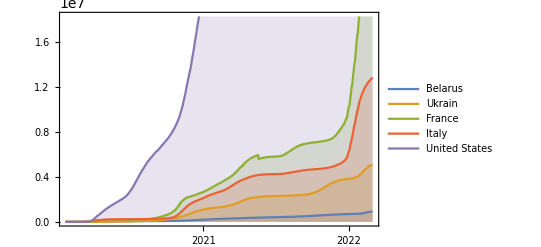

```mathematica
DateListPlot[{MapThread[{#1,#2}&,{dates,valuesBel}],MapThread[{#1,#2}&,{dates,valuesUkr}],MapThread[{#1,#2}&,{dates,valuesFr}],MapThread[{#1,#2}&,{dates,valuesIt}],MapThread[{#1,#2}&,{dates,valuesUS}]},Filling->Bottom,PlotLegends->{"Belarus","Ukrain","France","Italy","United States"}]
```

```mathematica
(*Хочу получать первую цифру каждого числа*)
valuesAfg=data⟦All,3⟧/.""->0//Rest;
```

```mathematica
n=valuesAfg[[56]]
```

26.

```mathematica
While[And[n!=1,n!=2,n!=3,n!=4,n!=5,n!=6,n!=7,n!=8,n!=9],n=Quotient[n,10]]
n
```

2

```mathematica
(*Теперь в функцию*)
getFirstNum[n_]:=Block[{num=n},While[And[num!=1,num!=2,num!=3,num!=4,num!=5,num!=6,num!=7,num!=8,num!=9,num!=0],num=Quotient[num,10]];Return[num]]
```

```mathematica
firstDigits=getFirstNum[#]&/@valuesAfg
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,5.,8.,8.,8.,8.,1,1,1,1,2,2,2,2,2,2,2,3,4,4,7,8,9,1,1,1,1,1,2,2,2,2,3,3,4,4,5,5,5,6,6,7,7,8,9,9,9,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,3,3,3,3,4,4,4,4,5,6,6,6,7,7,8,8,9,9,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,9,9,9,9,9,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
totalAmount=Length[firstDigits]
firstDigitsSorted=Sort[Tally[firstDigits]]//Rest
```

771

{{1,290},{2,34},{3,117},{4,74},{5,139},{5.,12},{6,32},{7,14},{8,11},{8.,4},{9,11}}

```mathematica
{#,firstDigitsSorted[[#,2]]/totalAmount*100//N}&/@Range[1,9]
```

{{1,37.6135},{2,4.40986},{3,15.1751},{4,9.59792},{5,18.0285},{6,1.55642},{7,4.15045},{8,1.81582},{9,1.42672}}

```mathematica
getBenford[list_]:=Block[{firstDigitsSorted=Sort[Tally[getFirstNum[#]&/@list]]//Rest,totalAmount=Length[firstDigits]},{#,firstDigitsSorted[[#,2]]/totalAmount*100//N}&/@Range[1,9]]
```

```mathematica
BenfordAfg=getBenford[valuesAfg]
BenfordBel=getBenford[valuesBel]
BenfordUkr=getBenford[valuesUkr]
BenfordFr=getBenford[valuesFr]
BenfordIt=getBenford[valuesIt]
BenfordUS=getBenford[valuesUS]
```

{{1,37.6135},{2,4.40986},{3,15.1751},{4,9.59792},{5,18.0285},{6,1.55642},{7,4.15045},{8,1.81582},{9,1.42672}}

{{1,10.5058},{2,0.648508},{3,10.8949},{4,13.489},{5,14.2672},{6,9.20882},{7,15.8236},{8,0.77821},{9,11.5435}}

{{1,24.5136},{2,1.29702},{3,30.9987},{4,15.1751},{5,0.389105},{6,7.5227},{7,4.28016},{8,2.85344},{9,2.59403}}

{{1,20.2335},{2,22.179},{3,0.129702},{4,8.69001},{5,0.389105},{6,6.61479},{7,0.129702},{8,15.6939},{9,0.389105}}

{{1,15.1751},{2,29.1829},{3,0.907912},{4,11.0246},{5,1.81582},{6,29.0532},{7,5.31777},{8,1.81582},{9,1.55642}}

{{1,0.259403},{2,15.3048},{3,0.259403},{4,24.1245},{5,15.9533},{6,7.26329},{7,0.389105},{8,5.57717},{9,0.259403}}

```mathematica
BenfordBar[list_]:=BarChart[list[[#,2]]&/@Range[1,9],ChartLabels->{"1","2","3","4","5","6","7","8","9"},ChartStyle->"Pastel"]
```

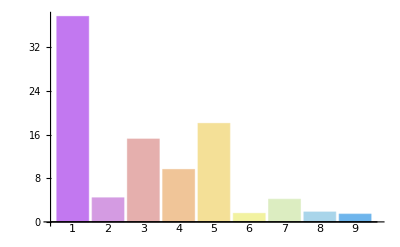

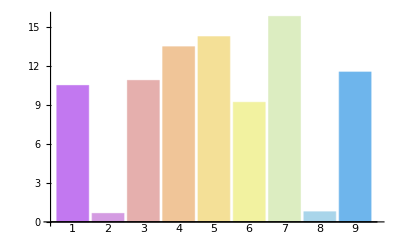

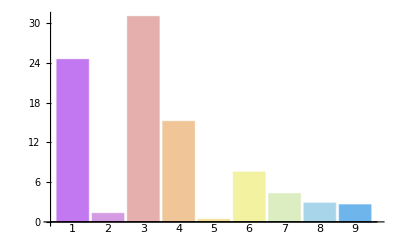

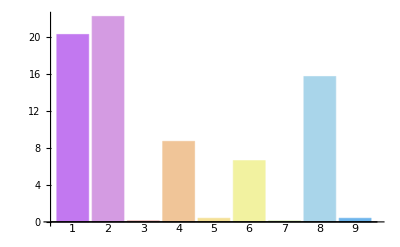

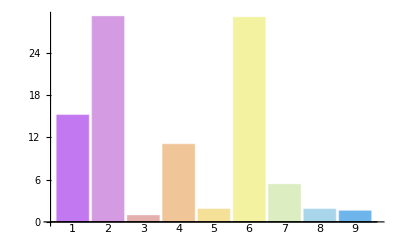

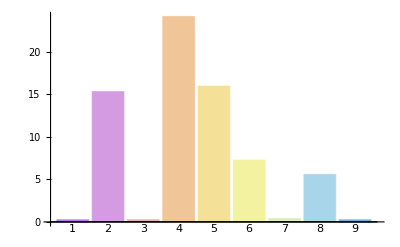

```mathematica
BenfordBar[BenfordAfg]
BenfordBar[BenfordBel]
BenfordBar[BenfordUkr]
BenfordBar[BenfordFr]
BenfordBar[BenfordIt]
BenfordBar[BenfordUS]
```